# El oscilador armónico amortiguado

Las ecuaciones de movimiento son:


Fijamos  y variamos  y vemos las trayectorias:

```mathematica
Manipulate[StreamPlot[{y,-(ω^2)*Sin[x]-y},{x,-5,5},{y,-2,2},FrameLabel->{x,y},AspectRatio->1/2],{ω,0,1}]
```

Cuenca de atracción de los espirales estables:

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==-9*Sin[x[t]]-y[t]/5,x[1000]==Pi+0.001*(-0.32240735599563636),y[1000]==0.001},{x,y},{t,0,1000}];
```

```mathematica
sol2=NDSolve[{x'[t]==y[t],y'[t]==-9*Sin[x[t]]-y[t]/5,x[1000]==-Pi+0.001*(-0.32240735599563636),y[1000]==0.001},{x,y},{t,0,1000}];
```

```mathematica
sol3=NDSolve[{x'[t]==y[t],y'[t]==-9*Sin[x[t]]-y[t]/5,x[1000]==-Pi-0.001*(-0.32240735599563636),y[1000]==-0.001},{x,y},{t,0,1000}];
```

```mathematica
sol4=NDSolve[{x'[t]==y[t],y'[t]==-9*Sin[x[t]]-y[t]/5,x[1000]==Pi-0.001*(-0.32240735599563636),y[1000]==-0.001},{x,y},{t,0,1000}];
```

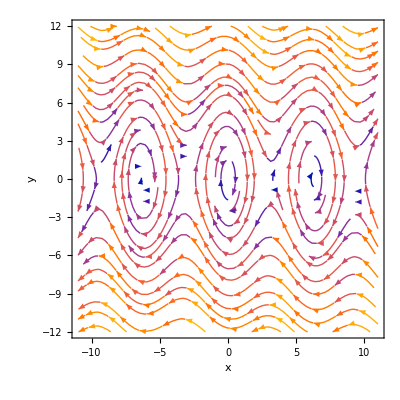

```mathematica
Show[{StreamPlot[{y,-9*Sin[x]-y/5},{x,-3*Pi-Pi/2,3*Pi+Pi/2},{y,-12,12},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,500,1000},PlotStyle->{Thick,Blue},PlotPoints->500],ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,500,1000},PlotStyle->{Thick,Blue},PlotPoints->500],ParametricPlot[Evaluate[{x[t],y[t]}/.sol3],{t,0,1000},PlotStyle->{Thick,Blue},PlotPoints->500],ParametricPlot[Evaluate[{x[t],y[t]}/.sol4],{t,0,1000},PlotStyle->{Thick,Blue},PlotPoints->500]}]
```

```mathematica
j=({{0, 1}, {-9*Cos[x], -1/5}});
```

```mathematica
N[Eigensystem[j/.{x->Pi,y->0}]]
```

{{-3.10167,2.90167},{{-0.322407,1.},{0.34463,1.}}}

```mathematica
N[Eigensystem[{{0,1},{9,-1/5}}]]
```

{{-3.10167,2.90167},{{-0.322407,1.},{0.34463,1.}}}